# AMS-511 Foundations of Quantitative Finance

## Fall 2018 — Assignment 10

Robert J. Frey, Research Professor
Stony Brook University, Applied Mathematics and Statistics

Robert.Frey@StonyBrook.edu
http://www.ams.sunysb.edu/~frey

## Question 01

Using the code provided in the class notes as a start, use Monte Carlo simulation to estimate the value of a European put with strike price K=100 and expiry T=0.75 for a non-dividend paying stock with current price S(0)=105.25 and volatility σ=0.35. The risk-free rate is r=0.01.

Write a function xEuroPutOptMonteCarlo[] to estimate the value of a European put.

```mathematica
xEuroPutOptMonteCarlo[nNowPrice_,nVolatility_,nStrikePrice_,nExpiry_,nRiskFree_,iSamples_]:={Mean[#],StandardDeviation[#]/√iSamples}&[Exp[-nRiskFree nExpiry](Max[nStrikePrice-#,0]&/@(nNowPrice Exp[(nRiskFree-nVolatility^2/2.)nExpiry]Exp[ nVolatility RandomVariate[NormalDistribution[0,√nExpiry],iSamples]]))];
```

Run a simulation for the option above. Use n=1000 samples.

```mathematica
sol = xEuroPutOptMonteCarlo[105.25, 0.35, 100, 0.75, 0.01, 1000]
```

{9.22001,0.42945}

Compute the mean estimate and a 95% confidence limit for the estimate.

```mathematica
{sol⟦1⟧-1.96sol⟦2⟧, sol⟦1⟧, sol⟦1⟧+1.96sol⟦2⟧}
```

{8.37829,9.22001,10.0617}

Use FinancialDerivative[] to compute the value of the option and compare it to the Monte Carlo result.

```mathematica
FinancialDerivative[{"European","Put"}, {"StrikePrice"-> 100.00, "Expiration"->0.75},  {"InterestRate"-> 0.01, "Volatility" -> 0.35, "CurrentPrice"-> 105.25}]
```

9.54695

The simulated price of 9.22001 is close to the price of 9.54695 calculated by financial derivative. The calculated price is within the simulated 95% confidence interval.

## Question 02

Consider the cash-chooser European option where the holder has the right at expiry to exercise an option or receive a fixed cash payment. In the class notes we worked through the pricing of a call cash-chooser. For this assignment.

Work out the pricing of a cash-chooser European put option using similar logic.

```mathematica
F(T)=max[K-S(T),B]
max[K-S(T),B]=max[K-S(T)-B,B-B]+B=max[(K-B)-S(T),0]+B
F(0)=ⅇ^(-r T)Subscript[E, Q][max[(K-B)-S(T),0]]+ⅇ^(-r T)Subscript[E, Q][B]
F(0)=P(0|K-B,T)+B ⅇ^(-r T)
F(t)=P(t|K-B,T)+B ⅇ^(-r (T-t))for 0≤t≤T
```

Price a cash-chooser European put with strike price K=250, expiry T=0.5, and cash pay-out B=20 for a non-dividend paying stock with current price S(0)=245.25 and volatility σ=0.35. The risk-free rate is r=0.01.

```mathematica
FinancialDerivative[{"European","Put"}, {"StrikePrice"-> (250.-20.), "Expiration"->0.5},  {"InterestRate"-> 0.01, "Volatility" -> 0.35,"CurrentPrice"->245.25}]+ⅇ^(-0.01×0.5)20.
```

35.9485

```mathematica
FinancialDerivative[{"European","Put"}, {"StrikePrice"-> (250.), "Expiration"->0.5},  {"InterestRate"-> 0.01, "Volatility" -> 0.35,"CurrentPrice"->245.25}]
```

26.1164

## Question 03

Consider a non-dividend paying stock with current price S(0)=105.25 and volatility σ=0.35. The risk-free rate is r=0.01. For puts and calls on this underlying with strike price K=100 and expiry T=0.75, use FinancialDerivative[] to numerically verify put-call parity holds.

```mathematica
call = FinancialDerivative[{"European","Call"}, {"StrikePrice"-> (100), "Expiration"->0.75},  {"InterestRate"-> 0.01, "Volatility" -> 0.35,"CurrentPrice"->105.25}]
put =FinancialDerivative[{"European","Put"}, {"StrikePrice"-> (100), "Expiration"->0.75},  {"InterestRate"-> 0.01, "Volatility" -> 0.35,"CurrentPrice"->105.25}]
105.25 == call - put + ⅇ^(-0.01×0.75)100.
```

15.5441

9.54695

True

## Question 04

An investor is given a payment in the form of a stock distribution with current price S(0)=200 and volatility σ=0.4 with the requirement that the investor has to hold onto the stock for 6 months. Concerned about the possibility that the stock will fall during this holding period, the investor buys a put option with strike K=150 and expiry T=0.5 as insurance. Assume the risk-free rate is r=0.01. Using the current price as the basis what is the profit or loss per share of the investor’s combined position as a function of S(T) at the close of the six-month holding period? (Hint: Don’t forget to factor in the initial cost of the option.)

3.78442

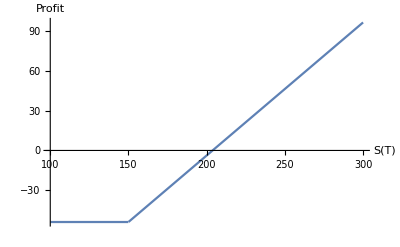

```mathematica
initialCost =FinancialDerivative[{"European","Put"}, {"StrikePrice"-> (150), "Expiration"->0.5},  {"InterestRate"-> 0.01, "Volatility" -> 0.4,"CurrentPrice"->200.}]
xProfit[expiryPrice]:=Max[expiryPrice, 150]-200-initialCost;
Plot[xProfit[s],{s,100, 300}, AxesLabel->{"S(T)","Profit"}]
```

## Question 05

You have a non-dividend paying stock with current price S(0)=105.25. The risk-free rate is r=0.02. A vanilla European put on this underlying with strike price K=100 and expiry T=0.75 is valued in the market at 9.19.

What is the implied volatility of the option?

```mathematica
impliedVolatility = FinancialDerivative[{"European","Put"},{"StrikePrice"->100,"Expiration"->0.75},{"CurrentPrice"->105.25,"InterestRate"->0.02,"Value"->9.19},"ImpliedVolatility"]
```

0.349935

The holder of the option is concerned about a rise in interest rates. How sensitive is the price of the option to changes in rate?

```mathematica
FinancialDerivative[{"European","Put"},{"StrikePrice"->100,"Expiration"->0.75},{"CurrentPrice"->105.25,"Volatility"->impliedVolatility,"InterestRate"->0.02},"Rho"]
```

-34.9738

Option price decreases by 34.9738 for each 1% increase in rate.

What would estimate the price of a call option on the same underlying with the same option parameter except an expiry T=0.5?

```mathematica
FinancialDerivative[{"European","Call"},{"StrikePrice"->100,"Expiration"->0.5},{"CurrentPrice"->105.25,"Volatility"->impliedVolatility,"InterestRate"->0.02}]
```

13.4824